# Van der Waals Interactions

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publication T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.131145,2.65486,2.64165,1.34807,1.34642, 0.0165192,0.0165437,0};
Subscript[δ, 2]={0.195,0.280,0.318,-0.603,-0.545, -0.085,-0.086,0}; (*Meschede values*)

(*Subscript[δ, 0]={3.131804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};*)
(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg\Spectres VdW\radinte\radinte.exe",8,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267757

-0.0267757

0.00739872

{0.,0.00741686}

### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=56; Subscript[n, max]=67;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]
NList
NList[[Ordering[NList[[All,{1}]]]]];
```

-1.01724×10^12

{0.156,Null}

341

{{56,3,5/2,1/2,-1.04967×10^12,-1},{56,3,7/2,1/2,-1.04967×10^12,-1},{56,4,7/2,1/2,-1.04905×10^12,1},{56,4,9/2,1/2,-1.04905×10^12,1},{56,5,9/2,1/2,-1.04905×10^12,-1},{56,5,11/2,1/2,-1.04905×10^12,-1},{56,6,11/2,1/2,-1.04905×10^12,1},{56,6,13/2,1/2,-1.04905×10^12,1},{56,7,13/2,1/2,-1.04905×10^12,-1},{56,7,15/2,1/2,-1.04905×10^12,-1},{56,8,15/2,1/2,-1.04905×10^12,1},{56,8,17/2,1/2,-1.04905×10^12,1},{56,9,17/2,1/2,-1.04905×10^12,-1},{56,9,19/2,1/2,-1.04905×10^12,-1},{56,10,19/2,1/2,-1.04905×10^12,1},{56,10,21/2,1/2,-1.04905×10^12,1},{56,11,21/2,1/2,-1.04905×10^12,-1},{56,11,23/2,1/2,-1.04905×10^12,-1},{56,12,23/2,1/2,-1.04905×10^12,1},{56,12,25/2,1/2,-1.04905×10^12,1},{56,13,25/2,1/2,-1.04905×10^12,-1},{56,13,27/2,1/2,-1.04905×10^12,-1},{56,14,27/2,1/2,-1.04905×10^12,1},{56,14,29/2,1/2,-1.04905×10^12,1},{56,15,29/2,1/2,-1.04905×10^12,-1},{56,15,31/2,1/2,-1.04905×10^12,-1},{56,16,31/2,1/2,-1.04905×10^12,1},{56,16,33/2,1/2,-1.04905×10^12,1},{56,17,33/2,1/2,-1.04905×10^12,-1},{56,17,35/2,1/2,-1.04905×10^12,-1},{56,18,35/2,1/2,-1.04905×10^12,1},{56,18,37/2,1/2,-1.04905×10^12,1},{56,19,37/2,1/2,-1.04905×10^12,-1},{56,19,39/2,1/2,-1.04905×10^12,-1},{56,20,39/2,1/2,-1.04905×10^12,1},{56,20,41/2,1/2,-1.04905×10^12,1},{56,21,41/2,1/2,-1.04905×10^12,-1},{56,21,43/2,1/2,-1.04905×10^12,-1},{56,22,43/2,1/2,-1.04905×10^12,1},{56,22,45/2,1/2,-1.04905×10^12,1},{56,23,45/2,1/2,-1.04905×10^12,-1},{56,23,47/2,1/2,-1.04905×10^12,-1},{56,24,47/2,1/2,-1.04905×10^12,1},{56,24,49/2,1/2,-1.04905×10^12,1},{56,25,49/2,1/2,-1.04905×10^12,-1},{56,25,51/2,1/2,-1.04905×10^12,-1},{56,26,51/2,1/2,-1.04905×10^12,1},{56,26,53/2,1/2,-1.04905×10^12,1},{56,27,53/2,1/2,-1.04905×10^12,-1},{56,27,55/2,1/2,-1.04905×10^12,-1},{56,28,55/2,1/2,-1.04905×10^12,1},{56,28,57/2,1/2,-1.04905×10^12,1},{56,29,57/2,1/2,-1.04905×10^12,-1},{56,29,59/2,1/2,-1.04905×10^12,-1},{56,30,59/2,1/2,-1.04905×10^12,1},{56,30,61/2,1/2,-1.04905×10^12,1},{56,31,61/2,1/2,-1.04905×10^12,-1},{56,31,63/2,1/2,-1.04905×10^12,-1},{56,32,63/2,1/2,-1.04905×10^12,1},{56,32,65/2,1/2,-1.04905×10^12,1},{56,33,65/2,1/2,-1.04905×10^12,-1},{56,33,67/2,1/2,-1.04905×10^12,-1},{56,34,67/2,1/2,-1.04905×10^12,1},{56,34,69/2,1/2,-1.04905×10^12,1},{56,35,69/2,1/2,-1.04905×10^12,-1},{56,35,71/2,1/2,-1.04905×10^12,-1},{56,36,71/2,1/2,-1.04905×10^12,1},{56,36,73/2,1/2,-1.04905×10^12,1},{56,37,73/2,1/2,-1.04905×10^12,-1},{56,37,75/2,1/2,-1.04905×10^12,-1},{56,38,75/2,1/2,-1.04905×10^12,1},{56,38,77/2,1/2,-1.04905×10^12,1},{56,39,77/2,1/2,-1.04905×10^12,-1},{56,39,79/2,1/2,-1.04905×10^12,-1},{56,40,79/2,1/2,-1.04905×10^12,1},{56,40,81/2,1/2,-1.04905×10^12,1},{56,41,81/2,1/2,-1.04905×10^12,-1},{56,41,83/2,1/2,-1.04905×10^12,-1},{56,42,83/2,1/2,-1.04905×10^12,1},{56,42,85/2,1/2,-1.04905×10^12,1},{56,43,85/2,1/2,-1.04905×10^12,-1},{56,43,87/2,1/2,-1.04905×10^12,-1},{56,44,87/2,1/2,-1.04905×10^12,1},{56,44,89/2,1/2,-1.04905×10^12,1},{56,45,89/2,1/2,-1.04905×10^12,-1},{56,45,91/2,1/2,-1.04905×10^12,-1},{56,46,91/2,1/2,-1.04905×10^12,1},{56,46,93/2,1/2,-1.04905×10^12,1},{56,47,93/2,1/2,-1.04905×10^12,-1},{56,47,95/2,1/2,-1.04905×10^12,-1},{56,48,95/2,1/2,-1.04905×10^12,1},{56,48,97/2,1/2,-1.04905×10^12,1},{56,49,97/2,1/2,-1.04905×10^12,-1},{56,49,99/2,1/2,-1.04905×10^12,-1},{56,50,99/2,1/2,-1.04905×10^12,1},{56,50,101/2,1/2,-1.04905×10^12,1},{56,51,101/2,1/2,-1.04905×10^12,-1},{56,51,103/2,1/2,-1.04905×10^12,-1},{56,52,103/2,1/2,-1.04905×10^12,1},{56,52,105/2,1/2,-1.04905×10^12,1},{56,53,105/2,1/2,-1.04905×10^12,-1},{56,53,107/2,1/2,-1.04905×10^12,-1},{56,54,107/2,1/2,-1.04905×10^12,1},{56,54,109/2,1/2,-1.04905×10^12,1},{56,55,109/2,1/2,-1.04905×10^12,-1},{56,55,111/2,1/2,-1.04905×10^12,-1},{57,2,3/2,1/2,-1.06221×10^12,1},{57,2,5/2,1/2,-1.06214×10^12,1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,4,7/2,1/2,-1.01256×10^12,1},{57,4,9/2,1/2,-1.01256×10^12,1},{57,5,9/2,1/2,-1.01256×10^12,-1},{57,5,11/2,1/2,-1.01256×10^12,-1},{57,6,11/2,1/2,-1.01256×10^12,1},{57,6,13/2,1/2,-1.01256×10^12,1},{57,7,13/2,1/2,-1.01256×10^12,-1},{57,7,15/2,1/2,-1.01256×10^12,-1},{57,8,15/2,1/2,-1.01256×10^12,1},{57,8,17/2,1/2,-1.01256×10^12,1},{57,9,17/2,1/2,-1.01256×10^12,-1},{57,9,19/2,1/2,-1.01256×10^12,-1},{57,10,19/2,1/2,-1.01256×10^12,1},{57,10,21/2,1/2,-1.01256×10^12,1},{57,11,21/2,1/2,-1.01256×10^12,-1},{57,11,23/2,1/2,-1.01256×10^12,-1},{57,12,23/2,1/2,-1.01256×10^12,1},{57,12,25/2,1/2,-1.01256×10^12,1},{57,13,25/2,1/2,-1.01256×10^12,-1},{57,13,27/2,1/2,-1.01256×10^12,-1},{57,14,27/2,1/2,-1.01256×10^12,1},{57,14,29/2,1/2,-1.01256×10^12,1},{57,15,29/2,1/2,-1.01256×10^12,-1},{57,15,31/2,1/2,-1.01256×10^12,-1},{57,16,31/2,1/2,-1.01256×10^12,1},{57,16,33/2,1/2,-1.01256×10^12,1},{57,17,33/2,1/2,-1.01256×10^12,-1},{57,17,35/2,1/2,-1.01256×10^12,-1},{57,18,35/2,1/2,-1.01256×10^12,1},{57,18,37/2,1/2,-1.01256×10^12,1},{57,19,37/2,1/2,-1.01256×10^12,-1},{57,19,39/2,1/2,-1.01256×10^12,-1},{57,20,39/2,1/2,-1.01256×10^12,1},{57,20,41/2,1/2,-1.01256×10^12,1},{57,21,41/2,1/2,-1.01256×10^12,-1},{57,21,43/2,1/2,-1.01256×10^12,-1},{57,22,43/2,1/2,-1.01256×10^12,1},{57,22,45/2,1/2,-1.01256×10^12,1},{57,23,45/2,1/2,-1.01256×10^12,-1},{57,23,47/2,1/2,-1.01256×10^12,-1},{57,24,47/2,1/2,-1.01256×10^12,1},{57,24,49/2,1/2,-1.01256×10^12,1},{57,25,49/2,1/2,-1.01256×10^12,-1},{57,25,51/2,1/2,-1.01256×10^12,-1},{57,26,51/2,1/2,-1.01256×10^12,1},{57,26,53/2,1/2,-1.01256×10^12,1},{57,27,53/2,1/2,-1.01256×10^12,-1},{57,27,55/2,1/2,-1.01256×10^12,-1},{57,28,55/2,1/2,-1.01256×10^12,1},{57,28,57/2,1/2,-1.01256×10^12,1},{57,29,57/2,1/2,-1.01256×10^12,-1},{57,29,59/2,1/2,-1.01256×10^12,-1},{57,30,59/2,1/2,-1.01256×10^12,1},{57,30,61/2,1/2,-1.01256×10^12,1},{57,31,61/2,1/2,-1.01256×10^12,-1},{57,31,63/2,1/2,-1.01256×10^12,-1},{57,32,63/2,1/2,-1.01256×10^12,1},{57,32,65/2,1/2,-1.01256×10^12,1},{57,33,65/2,1/2,-1.01256×10^12,-1},{57,33,67/2,1/2,-1.01256×10^12,-1},{57,34,67/2,1/2,-1.01256×10^12,1},{57,34,69/2,1/2,-1.01256×10^12,1},{57,35,69/2,1/2,-1.01256×10^12,-1},{57,35,71/2,1/2,-1.01256×10^12,-1},{57,36,71/2,1/2,-1.01256×10^12,1},{57,36,73/2,1/2,-1.01256×10^12,1},{57,37,73/2,1/2,-1.01256×10^12,-1},{57,37,75/2,1/2,-1.01256×10^12,-1},{57,38,75/2,1/2,-1.01256×10^12,1},{57,38,77/2,1/2,-1.01256×10^12,1},{57,39,77/2,1/2,-1.01256×10^12,-1},{57,39,79/2,1/2,-1.01256×10^12,-1},{57,40,79/2,1/2,-1.01256×10^12,1},{57,40,81/2,1/2,-1.01256×10^12,1},{57,41,81/2,1/2,-1.01256×10^12,-1},{57,41,83/2,1/2,-1.01256×10^12,-1},{57,42,83/2,1/2,-1.01256×10^12,1},{57,42,85/2,1/2,-1.01256×10^12,1},{57,43,85/2,1/2,-1.01256×10^12,-1},{57,43,87/2,1/2,-1.01256×10^12,-1},{57,44,87/2,1/2,-1.01256×10^12,1},{57,44,89/2,1/2,-1.01256×10^12,1},{57,45,89/2,1/2,-1.01256×10^12,-1},{57,45,91/2,1/2,-1.01256×10^12,-1},{57,46,91/2,1/2,-1.01256×10^12,1},{57,46,93/2,1/2,-1.01256×10^12,1},{57,47,93/2,1/2,-1.01256×10^12,-1},{57,47,95/2,1/2,-1.01256×10^12,-1},{57,48,95/2,1/2,-1.01256×10^12,1},{57,48,97/2,1/2,-1.01256×10^12,1},{57,49,97/2,1/2,-1.01256×10^12,-1},{57,49,99/2,1/2,-1.01256×10^12,-1},{57,50,99/2,1/2,-1.01256×10^12,1},{57,50,101/2,1/2,-1.01256×10^12,1},{57,51,101/2,1/2,-1.01256×10^12,-1},{57,51,103/2,1/2,-1.01256×10^12,-1},{57,52,103/2,1/2,-1.01256×10^12,1},{57,52,105/2,1/2,-1.01256×10^12,1},{57,53,105/2,1/2,-1.01256×10^12,-1},{57,53,107/2,1/2,-1.01256×10^12,-1},{57,54,107/2,1/2,-1.01256×10^12,1},{57,54,109/2,1/2,-1.01256×10^12,1},{57,55,109/2,1/2,-1.01256×10^12,-1},{57,55,111/2,1/2,-1.01256×10^12,-1},{57,56,111/2,1/2,-1.01256×10^12,1},{57,56,113/2,1/2,-1.01256×10^12,1},{58,1,1/2,1/2,-1.07403×10^12,-1},{58,1,3/2,1/2,-1.07351×10^12,-1},{58,2,3/2,1/2,-1.02504×10^12,1},{58,2,5/2,1/2,-1.02498×10^12,1},{58,3,5/2,1/2,-9.78506×10^11,-1},{58,3,7/2,1/2,-9.78506×10^11,-1},{58,4,7/2,1/2,-9.77949×10^11,1},{58,4,9/2,1/2,-9.77949×10^11,1},{58,5,9/2,1/2,-9.77949×10^11,-1},{58,5,11/2,1/2,-9.77949×10^11,-1},{58,6,11/2,1/2,-9.77949×10^11,1},{58,6,13/2,1/2,-9.77949×10^11,1},{58,7,13/2,1/2,-9.77949×10^11,-1},{58,7,15/2,1/2,-9.77949×10^11,-1},{58,8,15/2,1/2,-9.77949×10^11,1},{58,8,17/2,1/2,-9.77949×10^11,1},{58,9,17/2,1/2,-9.77949×10^11,-1},{58,9,19/2,1/2,-9.77949×10^11,-1},{58,10,19/2,1/2,-9.77949×10^11,1},{58,10,21/2,1/2,-9.77949×10^11,1},{58,11,21/2,1/2,-9.77949×10^11,-1},{58,11,23/2,1/2,-9.77949×10^11,-1},{58,12,23/2,1/2,-9.77949×10^11,1},{58,12,25/2,1/2,-9.77949×10^11,1},{58,13,25/2,1/2,-9.77949×10^11,-1},{58,13,27/2,1/2,-9.77949×10^11,-1},{58,14,27/2,1/2,-9.77949×10^11,1},{58,14,29/2,1/2,-9.77949×10^11,1},{58,15,29/2,1/2,-9.77949×10^11,-1},{58,15,31/2,1/2,-9.77949×10^11,-1},{58,16,31/2,1/2,-9.77949×10^11,1},{58,16,33/2,1/2,-9.77949×10^11,1},{58,17,33/2,1/2,-9.77949×10^11,-1},{58,17,35/2,1/2,-9.77949×10^11,-1},{58,18,35/2,1/2,-9.77949×10^11,1},{58,18,37/2,1/2,-9.77949×10^11,1},{58,19,37/2,1/2,-9.77949×10^11,-1},{58,19,39/2,1/2,-9.77949×10^11,-1},{58,20,39/2,1/2,-9.77949×10^11,1},{58,20,41/2,1/2,-9.77949×10^11,1},{58,21,41/2,1/2,-9.77949×10^11,-1},{58,21,43/2,1/2,-9.77949×10^11,-1},{58,22,43/2,1/2,-9.77949×10^11,1},{58,22,45/2,1/2,-9.77949×10^11,1},{58,23,45/2,1/2,-9.77949×10^11,-1},{58,23,47/2,1/2,-9.77949×10^11,-1},{58,24,47/2,1/2,-9.77949×10^11,1},{58,24,49/2,1/2,-9.77949×10^11,1},{58,25,49/2,1/2,-9.77949×10^11,-1},{58,25,51/2,1/2,-9.77949×10^11,-1},{58,26,51/2,1/2,-9.77949×10^11,1},{58,26,53/2,1/2,-9.77949×10^11,1},{58,27,53/2,1/2,-9.77949×10^11,-1},{58,27,55/2,1/2,-9.77949×10^11,-1},{58,28,55/2,1/2,-9.77949×10^11,1},{58,28,57/2,1/2,-9.77949×10^11,1},{58,29,57/2,1/2,-9.77949×10^11,-1},{58,29,59/2,1/2,-9.77949×10^11,-1},{58,30,59/2,1/2,-9.77949×10^11,1},{58,30,61/2,1/2,-9.77949×10^11,1},{58,31,61/2,1/2,-9.77949×10^11,-1},{58,31,63/2,1/2,-9.77949×10^11,-1},{58,32,63/2,1/2,-9.77949×10^11,1},{58,32,65/2,1/2,-9.77949×10^11,1},{58,33,65/2,1/2,-9.77949×10^11,-1},{58,33,67/2,1/2,-9.77949×10^11,-1},{58,34,67/2,1/2,-9.77949×10^11,1},{58,34,69/2,1/2,-9.77949×10^11,1},{58,35,69/2,1/2,-9.77949×10^11,-1},{58,35,71/2,1/2,-9.77949×10^11,-1},{58,36,71/2,1/2,-9.77949×10^11,1},{58,36,73/2,1/2,-9.77949×10^11,1},{58,37,73/2,1/2,-9.77949×10^11,-1},{58,37,75/2,1/2,-9.77949×10^11,-1},{58,38,75/2,1/2,-9.77949×10^11,1},{58,38,77/2,1/2,-9.77949×10^11,1},{58,39,77/2,1/2,-9.77949×10^11,-1},{58,39,79/2,1/2,-9.77949×10^11,-1},{58,40,79/2,1/2,-9.77949×10^11,1},{58,40,81/2,1/2,-9.77949×10^11,1},{58,41,81/2,1/2,-9.77949×10^11,-1},{58,41,83/2,1/2,-9.77949×10^11,-1},{58,42,83/2,1/2,-9.77949×10^11,1},{58,42,85/2,1/2,-9.77949×10^11,1},{58,43,85/2,1/2,-9.77949×10^11,-1},{58,43,87/2,1/2,-9.77949×10^11,-1},{58,44,87/2,1/2,-9.77949×10^11,1},{58,44,89/2,1/2,-9.77949×10^11,1},{58,45,89/2,1/2,-9.77949×10^11,-1},{58,45,91/2,1/2,-9.77949×10^11,-1},{58,46,91/2,1/2,-9.77949×10^11,1},{58,46,93/2,1/2,-9.77949×10^11,1},{58,47,93/2,1/2,-9.77949×10^11,-1},{58,47,95/2,1/2,-9.77949×10^11,-1},{58,48,95/2,1/2,-9.77949×10^11,1},{58,48,97/2,1/2,-9.77949×10^11,1},{58,49,97/2,1/2,-9.77949×10^11,-1},{58,49,99/2,1/2,-9.77949×10^11,-1},{58,50,99/2,1/2,-9.77949×10^11,1},{58,50,101/2,1/2,-9.77949×10^11,1},{58,51,101/2,1/2,-9.77949×10^11,-1},{58,51,103/2,1/2,-9.77949×10^11,-1},{58,52,103/2,1/2,-9.77949×10^11,1},{58,52,105/2,1/2,-9.77949×10^11,1},{58,53,105/2,1/2,-9.77949×10^11,-1},{58,53,107/2,1/2,-9.77949×10^11,-1},{58,54,107/2,1/2,-9.77949×10^11,1},{58,54,109/2,1/2,-9.77949×10^11,1},{58,55,109/2,1/2,-9.77949×10^11,-1},{58,55,111/2,1/2,-9.77949×10^11,-1},{58,56,111/2,1/2,-9.77949×10^11,1},{58,56,113/2,1/2,-9.77949×10^11,1},{58,57,113/2,1/2,-9.77949×10^11,-1},{58,57,115/2,1/2,-9.77949×10^11,-1},{59,0,1/2,1/2,-1.05398×10^12,1},{59,1,1/2,1/2,-1.03624×10^12,-1},{59,1,3/2,1/2,-1.03576×10^12,-1},{59,2,3/2,1/2,-9.89787×10^11,1},{59,2,5/2,1/2,-9.89731×10^11,1},{60,0,1/2,1/2,-1.01724×10^12,1},{60,1,1/2,1/2,-1.00042×10^12,-1},{60,1,3/2,1/2,-9.99955×10^11,-1},{61,0,1/2,1/2,-9.82389×10^11,1},{61,1,1/2,1/2,-9.66416×10^11,-1},{61,1,3/2,1/2,-9.65979×10^11,-1}}

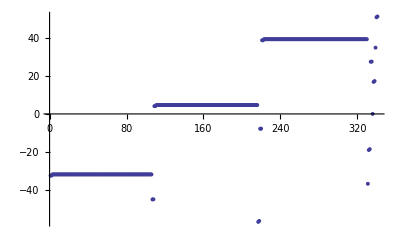

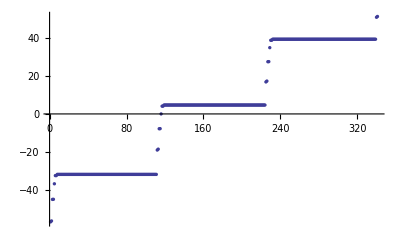

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;
(*Ordering NList beginning with highest Energy*)
LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]
(*Make List of Hilbert Space Basis level names for Plot of Energies*)
NList ;
LabelList;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

(*
MatrixPlot[AMatrix];
EV=Eigenvalues[VMatrix];
MatrixForm[Eigenvectors[VMatrix]];
MatrixPlot[Eigenvectors[VMatrix],ColorFunction->(GrayLevel[1-#1]&),ColorFunctionScaling->True];
*)

MatrixPlot[EMatrix];

(*Absolute Energies of disturbed levels:*)
Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ]
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
```

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{16.676,Null}

MatrixPlot::mat0: Argument {{{0, 0, 0}, {0, 0, 0}, {0., 0., 2322.61}, {0., 0., 0.}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, « 291 »}, {{0, 0, 0}, {0, 0, 0}, {0., 0., -74.4978}, {0., 0., 2332.15}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}, « 291 »}, « 48 », « 291 »} at position 1 is not a matrix.

{{300,-63.3829,58|1|1/2|1/2},{300,-60.6182,58|1|3/2|1/2},{300,-49.8906,57|2|3/2|1/2},{300,-49.6911,57|2|5/2|1/2},{300,-49.2398,59|0|1/2|1/2},{300,-49.0764,56|3|7/2|1/2},{300,-48.5922,56|3|5/2|1/2},{300,-48.4617,56|4|7/2|1/2},{300,-47.9442,56|4|9/2|1/2},{300,-47.8418,56|5|9/2|1/2},{300,-47.295,56|5|11/2|1/2},{300,-47.2147,56|6|11/2|1/2},{300,-46.6446,56|6|13/2|1/2},{300,-46.581,56|7|13/2|1/2},{300,-45.9933,56|7|15/2|1/2},{300,-45.942,56|8|15/2|1/2},{300,-45.3412,56|8|17/2|1/2},{300,-45.2991,56|9|17/2|1/2},{300,-44.6885,56|9|19/2|1/2},{300,-44.6533,56|10|19/2|1/2},{300,-44.0355,56|10|21/2|1/2},{300,-44.0055,56|11|21/2|1/2},{300,-43.3822,56|11|23/2|1/2},{300,-43.3563,56|12|23/2|1/2},{300,-42.7287,56|12|25/2|1/2},{300,-42.706,56|13|25/2|1/2},{300,-42.0752,56|13|27/2|1/2},{300,-42.0549,56|14|27/2|1/2},{300,-41.4217,56|14|29/2|1/2},{300,-41.4032,56|15|29/2|1/2},{300,-40.7685,56|15|31/2|1/2},{300,-40.7509,56|16|31/2|1/2},{300,-40.116,56|16|33/2|1/2},{300,-40.0983,56|17|33/2|1/2},{300,-39.4654,56|17|35/2|1/2},{300,-39.4453,56|18|35/2|1/2},{300,-38.8224,56|18|37/2|1/2},{300,-38.792,56|19|37/2|1/2},{300,-38.2523,56|19|39/2|1/2},{300,-38.1383,56|20|39/2|1/2},{300,-37.9931,56|20|41/2|1/2},{300,-37.4844,56|21|41/2|1/2},{300,-37.4563,56|21|43/2|1/2},{300,-36.8301,56|22|43/2|1/2},{300,-36.8151,56|22|45/2|1/2},{300,-36.1754,56|23|45/2|1/2},{300,-36.1641,56|23|47/2|1/2},{300,-35.5204,56|24|47/2|1/2},{300,-35.5104,56|24|49/2|1/2},{300,-34.865,56|25|49/2|1/2},{300,-34.8554,56|25|51/2|1/2},{300,-34.2093,56|26|51/2|1/2},{300,-34.1995,56|26|53/2|1/2},{300,-33.5531,56|27|53/2|1/2},{300,-33.543,56|27|55/2|1/2},{300,-32.8966,56|28|55/2|1/2},{300,-32.8858,56|28|57/2|1/2},{300,-32.2397,56|29|57/2|1/2},{300,-32.2282,56|29|59/2|1/2},{300,-31.5824,56|30|59/2|1/2},{300,-31.5701,56|30|61/2|1/2},{300,-30.9249,56|31|61/2|1/2},{300,-30.9116,56|31|63/2|1/2},{300,-30.267,56|32|63/2|1/2},{300,-30.2528,56|32|65/2|1/2},{300,-29.6089,56|33|65/2|1/2},{300,-29.5936,56|33|67/2|1/2},{300,-28.9504,56|34|67/2|1/2},{300,-28.934,56|34|69/2|1/2},{300,-28.2916,56|35|69/2|1/2},{300,-28.2739,56|35|71/2|1/2},{300,-27.6324,56|36|71/2|1/2},{300,-27.6135,56|36|73/2|1/2},{300,-26.9729,56|37|73/2|1/2},{300,-26.9526,56|37|75/2|1/2},{300,-26.3131,56|38|75/2|1/2},{300,-26.2913,56|38|77/2|1/2},{300,-25.6531,56|39|77/2|1/2},{300,-25.6296,56|39|79/2|1/2},{300,-24.9934,56|40|79/2|1/2},{300,-24.9679,56|40|81/2|1/2},{300,-24.3346,56|41|81/2|1/2},{300,-24.3066,56|41|83/2|1/2},{300,-23.6799,56|42|83/2|1/2},{300,-23.6476,56|42|85/2|1/2},{300,-23.0489,56|43|85/2|1/2},{300,-23.0004,56|43|87/2|1/2},{300,-22.6525,56|44|87/2|1/2},{300,-22.492,56|44|89/2|1/2},{300,-22.2702,56|45|89/2|1/2},{300,-22.2069,56|45|91/2|1/2},{300,-21.6413,56|46|91/2|1/2},{300,-21.6068,56|46|93/2|1/2},{300,-20.9843,56|47|93/2|1/2},{300,-20.9494,56|47|95/2|1/2},{300,-20.3213,56|48|95/2|1/2},{300,-20.2839,56|48|97/2|1/2},{300,-19.6555,56|49|97/2|1/2},{300,-19.6151,56|49|99/2|1/2},{300,-18.9877,56|50|99/2|1/2},{300,-18.9438,56|50|101/2|1/2},{300,-18.3181,56|51|101/2|1/2},{300,-18.27,56|51|103/2|1/2},{300,-17.6465,56|52|103/2|1/2},{300,-17.5933,56|52|105/2|1/2},{300,-16.9727,56|53|105/2|1/2},{300,-16.9129,56|53|107/2|1/2},{300,-16.2958,56|54|107/2|1/2},{300,-16.2271,56|54|109/2|1/2},{300,-15.6144,56|55|109/2|1/2},{300,-15.5323,56|55|111/2|1/2},{300,-14.9257,59|1|1/2|1/2},{300,-14.8178,59|1|3/2|1/2},{300,-13.5686,58|2|3/2|1/2},{300,-13.4428,58|2|5/2|1/2},{300,-12.8704,60|0|1/2|1/2},{300,-12.7756,57|3|7/2|1/2},{300,-12.1919,57|3|5/2|1/2},{300,-12.1159,57|4|7/2|1/2},{300,-11.5239,57|4|9/2|1/2},{300,-11.4622,57|5|9/2|1/2},{300,-10.8629,57|5|11/2|1/2},{300,-10.8132,57|6|11/2|1/2},{300,-10.2069,57|6|13/2|1/2},{300,-10.1672,57|7|13/2|1/2},{300,-9.55415,57|7|15/2|1/2},{300,-9.52282,57|8|15/2|1/2},{300,-8.90319,57|8|17/2|1/2},{300,-8.87835,57|9|17/2|1/2},{300,-8.25266,57|9|19/2|1/2},{300,-8.23255,57|10|19/2|1/2},{300,-7.60147,57|10|21/2|1/2},{300,-7.58462,57|11|21/2|1/2},{300,-6.94894,57|11|23/2|1/2},{300,-6.93419,57|12|23/2|1/2},{300,-6.29476,57|12|25/2|1/2},{300,-6.28122,57|13|25/2|1/2},{300,-5.63893,57|13|27/2|1/2},{300,-5.62583,57|14|27/2|1/2},{300,-4.98171,57|14|29/2|1/2},{300,-4.96823,57|15|29/2|1/2},{300,-4.32355,57|15|31/2|1/2},{300,-4.30867,57|16|31/2|1/2},{300,-3.66526,57|16|33/2|1/2},{300,-3.64742,57|17|33/2|1/2},{300,-3.00852,57|17|35/2|1/2},{300,-2.9847,57|18|35/2|1/2},{300,-2.35831,57|18|37/2|1/2},{300,-2.32072,57|19|37/2|1/2},{300,-1.73912,57|19|39/2|1/2},{300,-1.65566,57|20|39/2|1/2},{300,-1.28655,57|20|41/2|1/2},{300,-0.989667,57|21|41/2|1/2},{300,-0.878398,57|21|43/2|1/2},{300,-0.322859,57|22|43/2|1/2},{300,-0.274091,57|22|45/2|1/2},{300,0.344666,57|23|45/2|1/2},{300,0.376617,57|23|47/2|1/2},{300,1.01283,57|24|47/2|1/2},{300,1.03779,57|24|49/2|1/2},{300,1.68159,57|25|49/2|1/2},{300,1.70303,57|25|51/2|1/2},{300,2.3509,57|26|51/2|1/2},{300,2.37043,57|26|53/2|1/2},{300,3.02073,57|27|53/2|1/2},{300,3.03926,57|27|55/2|1/2},{300,3.69104,57|28|55/2|1/2},{300,3.70912,57|28|57/2|1/2},{300,4.36176,57|29|57/2|1/2},{300,4.37978,57|29|59/2|1/2},{300,5.03281,57|30|59/2|1/2},{300,5.05104,57|30|61/2|1/2},{300,5.7041,57|31|61/2|1/2},{300,5.72277,57|31|63/2|1/2},{300,6.37556,57|32|63/2|1/2},{300,6.39484,57|32|65/2|1/2},{300,7.04714,57|33|65/2|1/2},{300,7.06719,57|33|67/2|1/2},{300,7.7188,57|34|67/2|1/2},{300,7.73978,57|34|69/2|1/2},{300,8.39052,57|35|69/2|1/2},{300,8.41259,57|35|71/2|1/2},{300,9.06222,57|36|71/2|1/2},{300,9.0856,57|36|73/2|1/2},{300,9.73378,57|37|73/2|1/2},{300,9.75873,57|37|75/2|1/2},{300,10.4049,57|38|75/2|1/2},{300,10.4319,57|38|77/2|1/2},{300,11.0749,57|39|77/2|1/2},{300,11.1048,57|39|79/2|1/2},{300,11.7412,57|40|79/2|1/2},{300,11.7768,57|40|81/2|1/2},{300,12.3886,57|41|81/2|1/2},{300,12.4451,57|41|83/2|1/2},{300,12.8243,57|42|83/2|1/2},{300,13.0835,57|42|85/2|1/2},{300,13.1721,57|43|85/2|1/2},{300,13.3875,57|43|87/2|1/2},{300,13.805,57|44|87/2|1/2},{300,13.8437,57|44|89/2|1/2},{300,14.4707,57|45|89/2|1/2},{300,14.5027,57|45|91/2|1/2},{300,15.1422,57|46|91/2|1/2},{300,15.175,57|46|93/2|1/2},{300,15.8159,57|47|93/2|1/2},{300,15.8507,57|47|95/2|1/2},{300,16.4909,57|48|95/2|1/2},{300,16.5281,57|48|97/2|1/2},{300,17.167,57|49|97/2|1/2},{300,17.2069,57|49|99/2|1/2},{300,17.8443,57|50|99/2|1/2},{300,17.8872,57|50|101/2|1/2},{300,18.5227,57|51|101/2|1/2},{300,18.5691,57|51|103/2|1/2},{300,19.2024,57|52|103/2|1/2},{300,19.2528,57|52|105/2|1/2},{300,19.8837,57|53|105/2|1/2},{300,19.9389,57|53|107/2|1/2},{300,20.5669,57|54|107/2|1/2},{300,20.6274,57|54|109/2|1/2},{300,21.058,57|55|109/2|1/2},{300,21.1735,57|55|111/2|1/2},{300,21.258,57|56|111/2|1/2},{300,21.3257,57|56|113/2|1/2},{300,21.782,60|1|1/2|1/2},{300,21.8677,60|1|3/2|1/2},{300,21.9528,59|2|3/2|1/2},{300,22.033,59|2|5/2|1/2},{300,22.4867,61|0|1/2|1/2},{300,22.5574,58|3|7/2|1/2},{300,22.6521,58|3|5/2|1/2},{300,22.7594,58|4|7/2|1/2},{300,23.1835,58|4|9/2|1/2},{300,23.2455,58|5|9/2|1/2},{300,23.8635,58|5|11/2|1/2},{300,23.9201,58|6|11/2|1/2},{300,24.5385,58|6|13/2|1/2},{300,24.5899,58|7|13/2|1/2},{300,25.208,58|7|15/2|1/2},{300,25.2549,58|8|15/2|1/2},{300,25.8725,58|8|17/2|1/2},{300,25.9154,58|9|17/2|1/2},{300,26.5331,58|9|19/2|1/2},{300,26.5724,58|10|19/2|1/2},{300,27.1913,58|10|21/2|1/2},{300,27.2273,58|11|21/2|1/2},{300,27.8486,58|11|23/2|1/2},{300,27.8818,58|12|23/2|1/2},{300,28.5066,58|12|25/2|1/2},{300,28.5374,58|13|25/2|1/2},{300,29.1664,58|13|27/2|1/2},{300,29.1954,58|14|27/2|1/2},{300,29.8286,58|14|29/2|1/2},{300,29.8563,58|15|29/2|1/2},{300,30.4931,58|15|31/2|1/2},{300,30.5201,58|16|31/2|1/2},{300,31.1596,58|16|33/2|1/2},{300,31.1867,58|17|33/2|1/2},{300,31.8274,58|17|35/2|1/2},{300,31.8557,58|18|35/2|1/2},{300,32.4954,58|18|37/2|1/2},{300,32.5267,58|19|37/2|1/2},{300,33.1617,58|19|39/2|1/2},{300,33.1993,58|20|39/2|1/2},{300,33.821,58|20|41/2|1/2},{300,33.8733,58|21|41/2|1/2},{300,34.4521,58|21|43/2|1/2},{300,34.5482,58|22|43/2|1/2},{300,34.9547,58|22|45/2|1/2},{300,35.224,58|23|45/2|1/2},{300,35.373,58|23|47/2|1/2},{300,35.9004,58|24|47/2|1/2},{300,35.9626,58|24|49/2|1/2},{300,36.5774,58|25|49/2|1/2},{300,36.6156,58|25|51/2|1/2},{300,37.2548,58|26|51/2|1/2},{300,37.2834,58|26|53/2|1/2},{300,37.9326,58|27|53/2|1/2},{300,37.9566,58|27|55/2|1/2},{300,38.6108,58|28|55/2|1/2},{300,38.6324,58|28|57/2|1/2},{300,39.2892,58|29|57/2|1/2},{300,39.3096,58|29|59/2|1/2},{300,39.9678,58|30|59/2|1/2},{300,39.9878,58|30|61/2|1/2},{300,40.6466,58|31|61/2|1/2},{300,40.6667,58|31|63/2|1/2},{300,41.3254,58|32|63/2|1/2},{300,41.3459,58|32|65/2|1/2},{300,42.0042,58|33|65/2|1/2},{300,42.0254,58|33|67/2|1/2},{300,42.683,58|34|67/2|1/2},{300,42.7051,58|34|69/2|1/2},{300,43.3617,58|35|69/2|1/2},{300,43.385,58|35|71/2|1/2},{300,44.0405,58|36|71/2|1/2},{300,44.0651,58|36|73/2|1/2},{300,44.7193,58|37|73/2|1/2},{300,44.7453,58|37|75/2|1/2},{300,45.398,58|38|75/2|1/2},{300,45.4259,58|38|77/2|1/2},{300,46.0768,58|39|77/2|1/2},{300,46.1066,58|39|79/2|1/2},{300,46.7555,58|40|79/2|1/2},{300,46.7876,58|40|81/2|1/2},{300,47.434,58|41|81/2|1/2},{300,47.4689,58|41|83/2|1/2},{300,48.1121,58|42|83/2|1/2},{300,48.1505,58|42|85/2|1/2},{300,48.7896,58|43|85/2|1/2},{300,48.8325,58|43|87/2|1/2},{300,49.4657,58|44|87/2|1/2},{300,49.5148,58|44|89/2|1/2},{300,50.1386,58|45|89/2|1/2},{300,50.1974,58|45|91/2|1/2},{300,50.8033,58|46|91/2|1/2},{300,50.8805,58|46|93/2|1/2},{300,51.4386,58|47|93/2|1/2},{300,51.564,58|47|95/2|1/2},{300,51.9511,58|48|95/2|1/2},{300,52.2479,58|48|97/2|1/2},{300,52.3818,58|49|97/2|1/2},{300,52.932,58|49|99/2|1/2},{300,52.9729,58|50|99/2|1/2},{300,53.616,58|50|101/2|1/2},{300,53.63,58|51|101/2|1/2},{300,54.2988,58|51|103/2|1/2},{300,54.3038,58|52|103/2|1/2},{300,54.9781,58|52|105/2|1/2},{300,54.9839,58|53|105/2|1/2},{300,55.6422,58|53|107/2|1/2},{300,55.6676,58|54|107/2|1/2},{300,56.2253,58|54|109/2|1/2},{300,56.3546,58|55|109/2|1/2},{300,56.6379,58|55|111/2|1/2},{300,57.0447,58|56|111/2|1/2},{300,57.1918,58|56|113/2|1/2},{300,57.7386,58|57|113/2|1/2},{300,57.8644,58|57|115/2|1/2},{300,58.4377,61|1|1/2|1/2},{300,58.5775,61|1|3/2|1/2}}

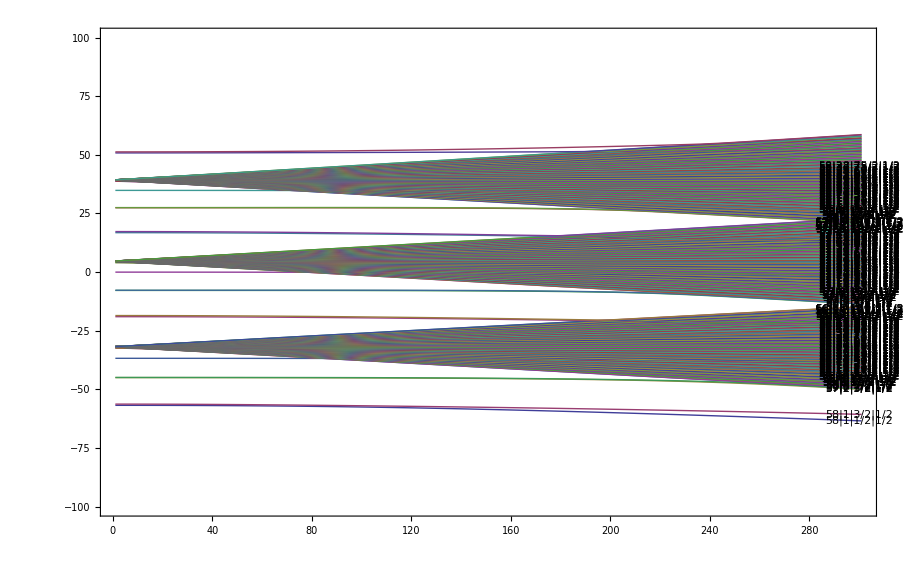

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

Show[ListPlot[MPList,Joined->True,PlotRange->{(*{Log[10,1/RMIN],Log[10,1/RMAX]}*)All,{-100,100}}(*All*),Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

57|29|59/2|1/2

57|30|59/2|1/2

{{1,4.67544},{2,4.67328},{3,4.67118},{4,4.66917},{5,4.66722},{6,4.66535},{7,4.66353},{8,4.66178},{9,4.66009},{10,4.65845},{11,4.65685},{12,4.65531},{13,4.6538},{14,4.65233},{15,4.65089},{16,4.64949},{17,4.64811},{18,4.64675},{19,4.64542},{20,4.64411},{21,4.64282},{22,4.64154},{23,4.64028},{24,4.63903},{25,4.6378},{26,4.63657},{27,4.63536},{28,4.63415},{29,4.63295},{30,4.63176},{31,4.63058},{32,4.6294},{33,4.62823},{34,4.62707},{35,4.62591},{36,4.62475},{37,4.6236},{38,4.62245},{39,4.62131},{40,4.62017},{41,4.61903},{42,4.6179},{43,4.61677},{44,4.61564},{45,4.61451},{46,4.61339},{47,4.61227},{48,4.61115},{49,4.61003},{50,4.60892},{51,4.6078},{52,4.60669},{53,4.60558},{54,4.60447},{55,4.60337},{56,4.60226},{57,4.60116},{58,4.60006},{59,4.59896},{60,4.59786},{61,4.59676},{62,4.59567},{63,4.59457},{64,4.59348},{65,4.59239},{66,4.59129},{67,4.5902},{68,4.58912},{69,4.58803},{70,4.58694},{71,4.58586},{72,4.58477},{73,4.58369},{74,4.58261},{75,4.58153},{76,4.58045},{77,4.57937},{78,4.57829},{79,4.57722},{80,4.57614},{81,4.57507},{82,4.57399},{83,4.57292},{84,4.57185},{85,4.57078},{86,4.56971},{87,4.56864},{88,4.56758},{89,4.56651},{90,4.56545},{91,4.56438},{92,4.56332},{93,4.56226},{94,4.5612},{95,4.56014},{96,4.55908},{97,4.55803},{98,4.55697},{99,4.55591},{100,4.55486},{101,4.55381},{102,4.55276},{103,4.55171},{104,4.55066},{105,4.54961},{106,4.54856},{107,4.54751},{108,4.54647},{109,4.54542},{110,4.54438},{111,4.54334},{112,4.5423},{113,4.54126},{114,4.54022},{115,4.53919},{116,4.53815},{117,4.53712},{118,4.53608},{119,4.53505},{120,4.53402},{121,4.53299},{122,4.53196},{123,4.53093},{124,4.52991},{125,4.52888},{126,4.52786},{127,4.52684},{128,4.52582},{129,4.5248},{130,4.52378},{131,4.52276},{132,4.52175},{133,4.52073},{134,4.51972},{135,4.51871},{136,4.5177},{137,4.51669},{138,4.51568},{139,4.51468},{140,4.51367},{141,4.51267},{142,4.51167},{143,4.51067},{144,4.50967},{145,4.50867},{146,4.50768},{147,4.50668},{148,4.50569},{149,4.5047},{150,4.50371},{151,4.50272},{152,4.50173},{153,4.50075},{154,4.49976},{155,4.49878},{156,4.4978},{157,4.49682},{158,4.49585},{159,4.49487},{160,4.4939},{161,4.49292},{162,4.49195},{163,4.49099},{164,4.49002},{165,4.48905},{166,4.48809},{167,4.48713},{168,4.48617},{169,4.48521},{170,4.48425},{171,4.4833},{172,4.48235},{173,4.4814},{174,4.48045},{175,4.4795},{176,4.47855},{177,4.47761},{178,4.47667},{179,4.47573},{180,4.47479},{181,4.47386},{182,4.47292},{183,4.47199},{184,4.47106},{185,4.47013},{186,4.46921},{187,4.46828},{188,4.46736},{189,4.46644},{190,4.46552},{191,4.46461},{192,4.46369},{193,4.46278},{194,4.46187},{195,4.46097},{196,4.46006},{197,4.45916},{198,4.45826},{199,4.45736},{200,4.45646},{201,4.45557},{202,4.45468},{203,4.45379},{204,4.4529},{205,4.45202},{206,4.45114},{207,4.45026},{208,4.44938},{209,4.4485},{210,4.44763},{211,4.44676},{212,4.44589},{213,4.44502},{214,4.44416},{215,4.4433},{216,4.44244},{217,4.44158},{218,4.44073},{219,4.43988},{220,4.43903},{221,4.43818},{222,4.43734},{223,4.4365},{224,4.43566},{225,4.43482},{226,4.43399},{227,4.43316},{228,4.43233},{229,4.4315},{230,4.43068},{231,4.42986},{232,4.42904},{233,4.42822},{234,4.42741},{235,4.4266},{236,4.42579},{237,4.42499},{238,4.42418},{239,4.42338},{240,4.42259},{241,4.42179},{242,4.421},{243,4.42021},{244,4.41943},{245,4.41864},{246,4.41786},{247,4.41708},{248,4.41631},{249,4.41553},{250,4.41476},{251,4.414},{252,4.41323},{253,4.41247},{254,4.41171},{255,4.41096},{256,4.4102},{257,4.40945},{258,4.4087},{259,4.40796},{260,4.40722},{261,4.40648},{262,4.40574},{263,4.40501},{264,4.40428},{265,4.40355},{266,4.40282},{267,4.4021},{268,4.40138},{269,4.40066},{270,4.39995},{271,4.39924},{272,4.39853},{273,4.39782},{274,4.39712},{275,4.39642},{276,4.39572},{277,4.39502},{278,4.39433},{279,4.39364},{280,4.39295},{281,4.39227},{282,4.39159},{283,4.39091},{284,4.39023},{285,4.38956},{286,4.38889},{287,4.38822},{288,4.38756},{289,4.38689},{290,4.38623},{291,4.38558},{292,4.38492},{293,4.38427},{294,4.38362},{295,4.38297},{296,4.38233},{297,4.38169},{298,4.38105},{299,4.38041},{300,4.37978},{301,4.37914}}

{{1,4.67772},{2,4.67783},{3,4.67801},{4,4.67826},{5,4.67857},{6,4.67895},{7,4.6794},{8,4.6799},{9,4.68045},{10,4.68105},{11,4.6817},{12,4.68239},{13,4.68312},{14,4.68389},{15,4.68469},{16,4.68552},{17,4.68637},{18,4.68725},{19,4.68815},{20,4.68907},{21,4.69001},{22,4.69097},{23,4.69194},{24,4.69292},{25,4.69392},{26,4.69492},{27,4.69594},{28,4.69697},{29,4.698},{30,4.69905},{31,4.7001},{32,4.70115},{33,4.70221},{34,4.70328},{35,4.70436},{36,4.70543},{37,4.70652},{38,4.7076},{39,4.70869},{40,4.70979},{41,4.71088},{42,4.71198},{43,4.71309},{44,4.71419},{45,4.7153},{46,4.71641},{47,4.71752},{48,4.71864},{49,4.71975},{50,4.72087},{51,4.72199},{52,4.72312},{53,4.72424},{54,4.72537},{55,4.72649},{56,4.72762},{57,4.72875},{58,4.72988},{59,4.73102},{60,4.73215},{61,4.73329},{62,4.73442},{63,4.73556},{64,4.7367},{65,4.73784},{66,4.73898},{67,4.74012},{68,4.74127},{69,4.74241},{70,4.74355},{71,4.7447},{72,4.74585},{73,4.74699},{74,4.74814},{75,4.74929},{76,4.75044},{77,4.75159},{78,4.75275},{79,4.7539},{80,4.75505},{81,4.75621},{82,4.75736},{83,4.75852},{84,4.75968},{85,4.76083},{86,4.76199},{87,4.76315},{88,4.76431},{89,4.76547},{90,4.76663},{91,4.76779},{92,4.76896},{93,4.77012},{94,4.77129},{95,4.77245},{96,4.77362},{97,4.77478},{98,4.77595},{99,4.77712},{100,4.77829},{101,4.77946},{102,4.78063},{103,4.7818},{104,4.78297},{105,4.78414},{106,4.78532},{107,4.78649},{108,4.78766},{109,4.78884},{110,4.79002},{111,4.79119},{112,4.79237},{113,4.79355},{114,4.79473},{115,4.79591},{116,4.79709},{117,4.79827},{118,4.79945},{119,4.80064},{120,4.80182},{121,4.803},{122,4.80419},{123,4.80538},{124,4.80656},{125,4.80775},{126,4.80894},{127,4.81013},{128,4.81132},{129,4.81251},{130,4.8137},{131,4.81489},{132,4.81608},{133,4.81728},{134,4.81847},{135,4.81967},{136,4.82087},{137,4.82206},{138,4.82326},{139,4.82446},{140,4.82566},{141,4.82686},{142,4.82806},{143,4.82926},{144,4.83047},{145,4.83167},{146,4.83287},{147,4.83408},{148,4.83529},{149,4.83649},{150,4.8377},{151,4.83891},{152,4.84012},{153,4.84133},{154,4.84254},{155,4.84376},{156,4.84497},{157,4.84619},{158,4.8474},{159,4.84862},{160,4.84984},{161,4.85105},{162,4.85227},{163,4.85349},{164,4.85471},{165,4.85594},{166,4.85716},{167,4.85838},{168,4.85961},{169,4.86084},{170,4.86206},{171,4.86329},{172,4.86452},{173,4.86575},{174,4.86698},{175,4.86821},{176,4.86945},{177,4.87068},{178,4.87192},{179,4.87315},{180,4.87439},{181,4.87563},{182,4.87687},{183,4.87811},{184,4.87935},{185,4.88059},{186,4.88184},{187,4.88308},{188,4.88433},{189,4.88558},{190,4.88682},{191,4.88807},{192,4.88932},{193,4.89058},{194,4.89183},{195,4.89308},{196,4.89434},{197,4.8956},{198,4.89685},{199,4.89811},{200,4.89937},{201,4.90063},{202,4.9019},{203,4.90316},{204,4.90442},{205,4.90569},{206,4.90696},{207,4.90823},{208,4.9095},{209,4.91077},{210,4.91204},{211,4.91331},{212,4.91459},{213,4.91587},{214,4.91714},{215,4.91842},{216,4.9197},{217,4.92098},{218,4.92227},{219,4.92355},{220,4.92484},{221,4.92612},{222,4.92741},{223,4.9287},{224,4.92999},{225,4.93129},{226,4.93258},{227,4.93388},{228,4.93517},{229,4.93647},{230,4.93777},{231,4.93907},{232,4.94037},{233,4.94168},{234,4.94298},{235,4.94429},{236,4.9456},{237,4.94691},{238,4.94822},{239,4.94953},{240,4.95085},{241,4.95216},{242,4.95348},{243,4.9548},{244,4.95612},{245,4.95744},{246,4.95877},{247,4.96009},{248,4.96142},{249,4.96275},{250,4.96408},{251,4.96541},{252,4.96674},{253,4.96808},{254,4.96941},{255,4.97075},{256,4.97209},{257,4.97343},{258,4.97478},{259,4.97612},{260,4.97747},{261,4.97882},{262,4.98017},{263,4.98152},{264,4.98287},{265,4.98423},{266,4.98558},{267,4.98694},{268,4.9883},{269,4.98966},{270,4.99103},{271,4.99239},{272,4.99376},{273,4.99513},{274,4.9965},{275,4.99787},{276,4.99925},{277,5.00062},{278,5.002},{279,5.00338},{280,5.00476},{281,5.00615},{282,5.00753},{283,5.00892},{284,5.01031},{285,5.0117},{286,5.0131},{287,5.01449},{288,5.01589},{289,5.01729},{290,5.01869},{291,5.02009},{292,5.0215},{293,5.0229},{294,5.02431},{295,5.02572},{296,5.02714},{297,5.02855},{298,5.02997},{299,5.03139},{300,5.03281},{301,5.03423}}

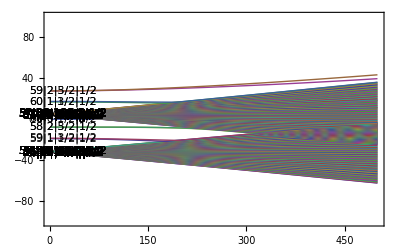

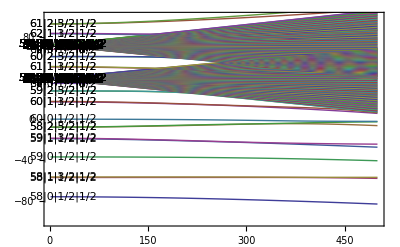

```mathematica
LabelList[[170]]
LabelList[[171]]

MPList[[170]]
MPList[[171]]
```

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

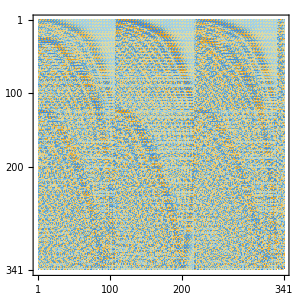

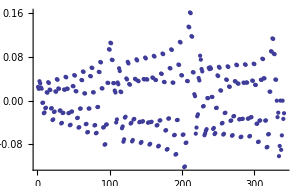

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

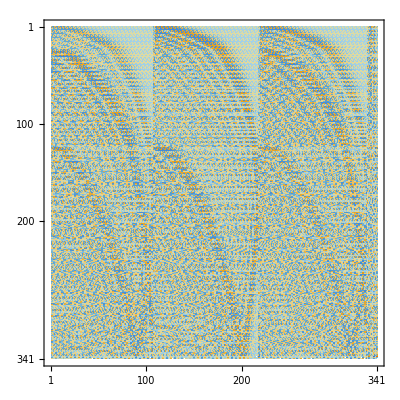

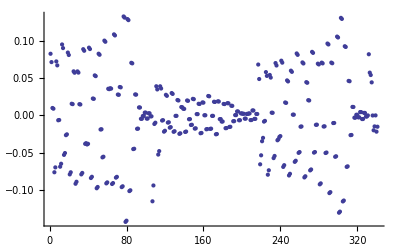

0.0478166

-13.5686

-7.79615

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```